# Parametric Sweep - Processing

## Last Updated: 24/03/2024

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

## General

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Dataset Processing

```mathematica
(*import raw counts and demodulate*)
ProcessDatasetCounts[filename_]:=Module[
{
(*actual data*)
dataset,
datasetFrequencies=Import[filename,{"/datasets/xArr"}],
datasetCounts=Import[filename,{"/datasets/results"}],
correlatedSignal,correlatedAmplitude,correlatedPhase,
(*parameters*)
modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],
(*processing*)
results
},

(*refine dataset*)
dataset=AssociationThread[datasetFrequencies->datasetCounts];
(*dataset=KeySort[dataset];*)

(*demodulate counts*)
correlatedSignal=KeyValueMap[
Total[Exp[ⅈ*(2*π*#1*1*^6)*#2]]/Length[#2]&,
dataset
];
{correlatedAmplitude,correlatedSignal}=Transpose[AbsArg[correlatedSignal]];

(*format data*)
results=Transpose[
{datasetFrequencies,ConstantArray[shimVoltage,Length[correlatedAmplitude]],##}&@@{correlatedAmplitude,correlatedSignal}
];

(*clean up mess*)
Remove[dataset,datasetFrequencies,datasetCounts];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
];
```

```mathematica
(*import already demodulated dataset*)
ProcessDataset[filename_]:=Module[
{
(*actual data*)
datasetRaw=Import[filename,{"/datasets/results"}],
(*parameters*)
(*modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],
shimVoltage=Import[filename,{"/datasets/dc_channel_voltage"}],*)
(*processing*)
results
},

(*refine dataset*)
(*dataset=KeySort[dataset];*)

(*format data*)
(*results=Transpose[
(datasetRaw[[;;,1]],ConstantArray[shimVoltage,Length[datasetRaw]],datasetRaw[[;;,3]],datasetRaw[[;;,4]]}
];*)
results=datasetRaw;

(*clean up mess*)
Remove[datasetRaw];
ClearSystemCache[];
ClearInOut[];

(*return dataset*)
Return[results];
];
```

# Iterative Plots

## Data

```mathematica
(*RandomReal[{55.,85.}]
RandomReal[{35.,65.}]*)
```

```mathematica
(*shimDataRF={
{58.6,60.49},
{42.34,69.6},
{46.62,77.57},
{55.28,68.74},
{50.52,72.24},
{52.49,69.32},
{51.38,70.62},
{51.7,70.23}
};
shimDataEGGS={
{58.6,78.63},
{49.14,69.6},
{46.62,63.65},
{50.91,68.74},
{50.52,69.10},
{52.49,71.32},
{51.81,70.62},
{51.7,70.42}
};*)
```

```mathematica
shimDataRF={
{76.64,50.},
{71.73,53.63},
{68.51,51.71}
};
shimDataEGGS={
{66.82,50.},
{71.73,55.27},
{68.68,51.71}
};
```

## Fit

```mathematica
(*fit*)
shimRFFit=LinearModelFit[shimDataRF,x,x];
shimEGGSFit=LinearModelFit[shimDataEGGS,x,x];
```

```mathematica
(*param table*)
shimRFFitParams=Style[
shimRFFit["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
shimEGGSFitParams=Style[
shimEGGSFit["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

```mathematica
(*extrapolate*)
xOpt=x/.First@NSolve[shimRFFit[x]==shimEGGSFit[x],{x}];
yOpt=Mean[{shimRFFit[xOpt],shimEGGSFit[xOpt]}];
```

## Plot

## Raw Data

```mathematica
shimDataPlot=ListPlot[
{shimDataRF,shimDataEGGS},
PlotRange->Full
(*Joined->{False,True,False,True}*),
FrameLabel->{ 
{Style["V Shim Voltage(V)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Algorithmic Shimming",{Black,Directive[15]}]
}
},
PlotLegends->{"RF Mode","EGGS Mode"}
];
```

```mathematica
shimDataPlotLines=ListLinePlot[
{shimDataRF,shimDataEGGS},
PlotRange->Full
(*Joined->{False,True,False,True}*),
FrameLabel->{ 
{Style["V Shim Voltage(V)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Algorithmic Shimming",{Black,Directive[15]}]
}
},
PlotStyle->{{Dashed},{Dashed}},
PlotLegends->{"RF Mode","EGGS Mode"}
];
```

## Callouts

```mathematica
shimCalloutsRF=Callout[
shimDataRF[[#]],
#,
Automatic(*Above*),
shimDataRF[[#]],
LabelStyle->Directive[15],
CalloutMarker->"Circle"
]&/@Range[Length[shimDataRF]];
shimCalloutsEGGS=Callout[
shimDataEGGS[[#]],
#,
Automatic(*Above*),
shimDataEGGS[[#]],
LabelStyle->Directive[15],
CalloutMarker->"Circle"
]&/@Range[Length[shimDataEGGS]];
```

```mathematica
shimCalloutPlot=ListPlot[
{shimCalloutsRF,shimCalloutsEGGS},
Joined->{False},
PlotRange->Full,
FrameLabel->{ 
{Style["V Shim Voltage(V)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Algorithmic Shimming",{Black,Directive[15]}]
}
},
PlotLegends->{"RF Mode","EGGS Mode"}
];
```

## Grid Lines

```mathematica
shimGridLines=Line[Transpose[{shimDataRF,shimDataEGGS}]];
shimGridLineGraphics=Graphics[{Red,Dashed,Thickness[0.01],shimGridLines},Background->White];
shimGridLinePlot=ListPlot[
{shimCalloutsRF,shimCalloutsEGGS},
Joined->{False},
PlotRange->Full,
FrameLabel->{ 
{Style["V Shim Voltage(V)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Algorithmic Shimming",{Black,Directive[15]}]
}
},
PlotLegends->{"RF Mode","EGGS Mode"},
Epilog->{{Red,Dashed,Thickness[0.005],shimGridLines}}
];
```

## Fitted Data

```mathematica
shimFitPlot=Plot[
{
shimRFFit[x],
shimEGGSFit[x]
},
{x,Min[shimDataRF[[;;,1]],shimDataEGGS[[;;,1]]],Max[shimDataRF[[;;,1]],shimDataEGGS[[;;,1]]]},
PlotRange->Full
(*Joined->{False,True,False,True}*),
FrameLabel->{ 
{Style["V Shim Voltage(V)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Algorithmic Shimming",{Black,Directive[15]}]
}
},
PlotLegends->{"RF Mode","EGGS Mode"}
];
```

## Show - Points

```mathematica
Print["Shim Opt. (V Shim, H Shim): ",yOpt," / ",xOpt];
{shimRFFitParams,shimEGGSFitParams}
Show[
shimGridLinePlot,
shimDataPlot,
shimFitPlot
]
```

Shim Opt. (V Shim, H Shim): 52.5456 / 69.2789

{ | Estimate | Standard Error | Confidence Interval
1 | 70.1408 | 26.3176 | {-264.257,404.538}
x | -0.253976 | 0.363651 | {-4.8746,4.36665}, | Estimate | Standard Error | Confidence Interval
1 | -22.4531 | 4.56477 | {-80.4541,35.5478}
x | 1.08256 | 0.0660543 | {0.243263,1.92186}}

-Graphics-

# Optima Plot

## Data

```mathematica
optimaData={
{58.6,77.7},
{58.9,69.6},
{46.62,67.20},
{49.84,68.74},
{50.22,69.22},
{52.02,70.62},
{51.63,70.48},
{51.7,70.4}
};
```

## Plot

```mathematica
optimaDataPlot=ListPlot[
{optimaData,optimaData},
Joined->{False,True,False},
PlotRange->Full,
FrameLabel->{ 
{Style["V Shim Voltage(V)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Extracted Optima",{Black,Directive[15]}]
}
}
];
```

```mathematica
optimaCallouts=Callout[
optimaData[[#]],
#,
Automatic(*Above*),
(*Automatic*)optimaData[[#]],
LabelStyle->Directive[15],
CalloutMarker->"Circle"
]&/@Range[Length[optimaData]];
```

```mathematica
optimaCalloutPlot=ListPlot[
optimaCallouts,
Joined->{False},
PlotRange->Full,
FrameLabel->{ 
{Style["V Shim Voltage(V)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Extracted Optima",{Black,Directive[15]}]
}
}
];
```

## Show

```mathematica
Show[
optimaCalloutPlot,
optimaDataPlot,
PlotRange->Full
]
```

-Graphics-

# TH

```mathematica
(52.35-49.57)/(70.30-70.60)
```

-9.26667

```mathematica
(50.60-50.84)/(70.30-70.60)
```

0.8

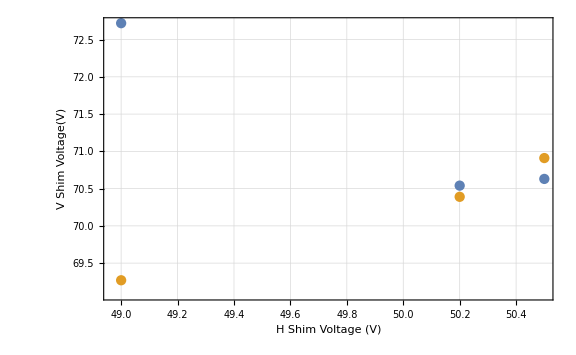

```mathematica
hsData={
{49.0,72.72,69.27},
{50.5,70.630,70.91},
{50.2,70.54,70.39}
};
hsDataRF=hsData[[;;,{1,2}]];
hsDataEGGS=hsData[[;;,{1,3}]];
ListPlot[
{hsDataRF,(*hsDataRF,hsDataEGGS,*)hsDataEGGS},
PlotRange->Full
(*Joined->{False,True,False,True}*),
FrameLabel->{ 
{Style["V Shim Voltage(V)",{Black,Directive[15]}],None},
{
Style["H Shim Voltage (V)",{Black,Directive[15]}],
Style["Normal Shimming (V Shim Sweep, H Shim Adjust)",{Black,Directive[15]}]
}
}
]
```

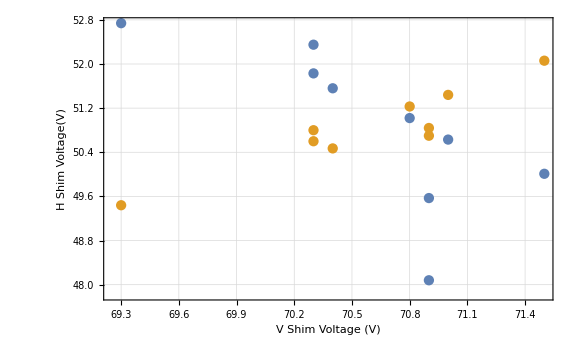

```mathematica
vsData={
{70.4,51.56,50.47},
{70.9,48.08,50.70},
{69.3,52.74,49.44},
{70.9,49.57,50.84},
{70.3,52.35,50.60},
{70.3,51.83,50.80},
{70.8,51.02,51.23},
{71.0,50.63,51.44},
{71.5,50.01,52.06}
};
vsDataRF=vsData[[;;,{1,2}]];
vsDataEGGS=vsData[[;;,{1,3}]];
ListPlot[
{vsDataRF,(*vsDataRF,vsDataEGGS,*)vsDataEGGS},
PlotRange->Full,
(*Joined->{False,True,False,True}*)
FrameLabel->{ 
{Style["H Shim Voltage(V)",{Black,Directive[15]}],None},
{
Style["V Shim Voltage (V)",{Black,Directive[15]}],
Style["Anti-Normal Shimming (H Shim Sweep, V Shim Adjust)",{Black,Directive[15]}]
}
}
]
```

# Att Curve Plot

## Data

```mathematica
voltComplexOffsetData={
{6.,8.2961},
{7.,8.0578},
{8.,7.6238},
{9.,5.555},
{10.,6.11179},
{11.,4.65004},
{12.,5.0714},
{13.,4.68811},
{14.,3.70603},
{15.,2.97492},
{16.,3.41409},
{17.,2.9136}
};
```

```mathematica
voltComplexSlopeData={
{6.,0.11925},
{7.,0.11582},
{8.,0.1093},
{9.,0.07988},
{10.,0.0873554},
{11.,0.06699},
{12.,0.072973},
{13.,0.0673},
{14.,0.05327},
{15.,0.04255},
{16.,0.0491},
{17.,0.041925}
};
```

```mathematica
rfAttData={
{18.,0.038,1274.36},
{17.,0.073,1273.84},
{16.,0.086,1273.79},
{15.,0.023,1274.15},
{14.,0.107,1273.89},
{13.,0.027,1274.32},
{12.,0.066,1274.32},
{11.,0.113,1273.82},
{10.,0.136,1273.79},
{9.,0.059,1273.89},
{8.,0.157,1274.23},
{7.,0.123,1274.13}
};
```

```mathematica
eggsAttData={
{18.,0.096,1565.90},
{17.,0.111,1565.67},
{16.,0.127,1565.95},
{15.,0.129,1565.99},
{14.,0.147,1565.81},
{13.,0.135,1566.01},
{12.,0.179,1565.79},
{11.,0.192,1565.78},
{10.,0.220,1565.82},
{9.,0.223,1565.80},
{8.,0.249,1565.80},
{7.,0.255,1566.14}
};
```

## Fit

```mathematica
eggsAttData=voltComplexSlopeData;
```

```mathematica
(*fit*)
rfAttFit=LinearModelFit[rfAttData[[;;,{1,2}]],x,x];
eggsAttFit=LinearModelFit[eggsAttData[[;;,{1,2}]],x,x];
```

```mathematica
(*param table*)
rfAttFitParams=Style[
rfAttFit["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
eggsAttFitParams=Style[
eggsAttFit["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
Abs[-0.0317522+-0.0273768ⅈ]
```

0.0419248

```mathematica
(*ListPlot[
{rfAttData[[;;,{1,3}]],
rfAttData[[;;,{1,3}]]
(*eggsAttData[[;;,{1,3}]],
eggsAttData[[;;,{1,3}]]*)},
PlotRange->Full,
Joined->{False,True,False,True},
FrameLabel->{ 
{Style["Secular Frequency (kHz)",{Black,Directive[15]}],None},
{
Style["Attenuation (dB)",{Black,Directive[15]}],
Style["Attenuation Dependence",{Black,Directive[15]}]
}
}
]*)
```

```mathematica
attDataPlot=ListPlot[
{
(*rfAttData[[;;,{1,2}]],*)
eggsAttData[[;;,{1,2}]]
},
PlotRange->Full,
Joined->{False,False},
FrameLabel->{ 
{Style["Correlated Amplitude Slope",{Black,Directive[15]}],None},
{
Style["Attenuation (dB)",{Black,Directive[15]}],
Style["Attenuation Dependence (Complex Voltage Slope)",{Black,Directive[15]}]
}
},
PlotLegends->{"RF Mode","EGGS Mode"}
];
```

```mathematica
attFitPlot=Plot[
{
(*rfAttFit[x],*)
eggsAttFit[x]
},
{x,Min[rfAttData[[;;,1]],eggsAttData[[;;,1]]],Max[rfAttData[[;;,1]],eggsAttData[[;;,1]]]},
PlotRange->Full
(*Joined->{False,True,False,True}*),
FrameLabel->{ 
{Style["Correlated Amplitude",{Black,Directive[15]}],None},
{
Style["Attenuation (dB)",{Black,Directive[15]}],
Style["Attenuation Dependence",{Black,Directive[15]}]
}
},
PlotLegends->{"RF Mode","EGGS Mode"}
];
```

## Show

<|EGGS→ | Estimate | Standard Error | Confidence Interval
1 | 0.160139 | 0.00804251 | {0.14222,0.178059}
x | -0.00736202 | 0.000669822 | {-0.00885448,-0.00586957}|>

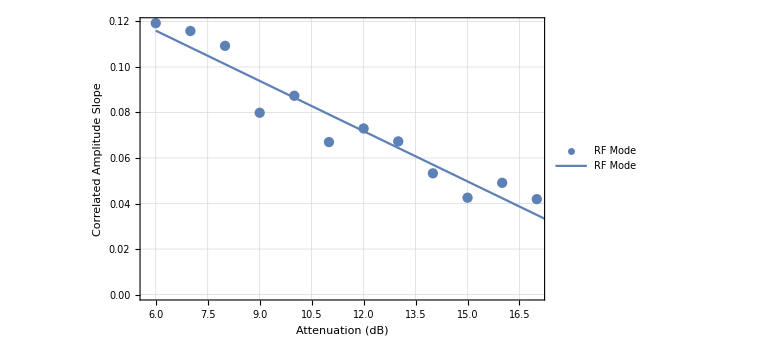

```mathematica
<|(*"RF"->rfAttFitParams,*)
"EGGS"->eggsAttFitParams|>
Show[
attDataPlot,
attFitPlot
]
```